# 2D Automatas

## Examples

### 3D View

```mathematica
gameOfLife={4320,{4,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
```

```mathematica
initialMatrix=RandomInteger[1,{5,5}];
```

```mathematica
Graphics3D[Cuboid/@Position[CellularAutomaton[gameOfLife,{initialMatrix,0},200],1],ViewVertical->{-1,0,0}]
```

-Graphics3D-

### $

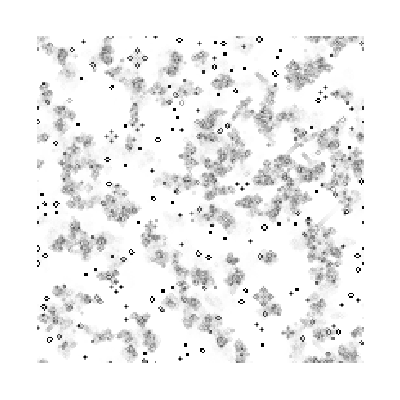

```mathematica
ArrayPlot[Mean[MapIndexed[#1*(1.07^-Last[#2])&,Reverse[CellularAutomaton["GameOfLife",RandomInteger[1,{200,200}],200]]]],FrameLabel->{None,StringTemplate["step ``"][200]}]
```

## Binarization of Rules

### K-3 Lists to Rule

```mathematica
k3ListsToRule[lists_?MatrixQ]:=FromDigits[Reverse[Join@@Transpose[lists]],3]
```

### Game of Life

```mathematica
IntegerDigits[224,2,18]
```

{0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0}

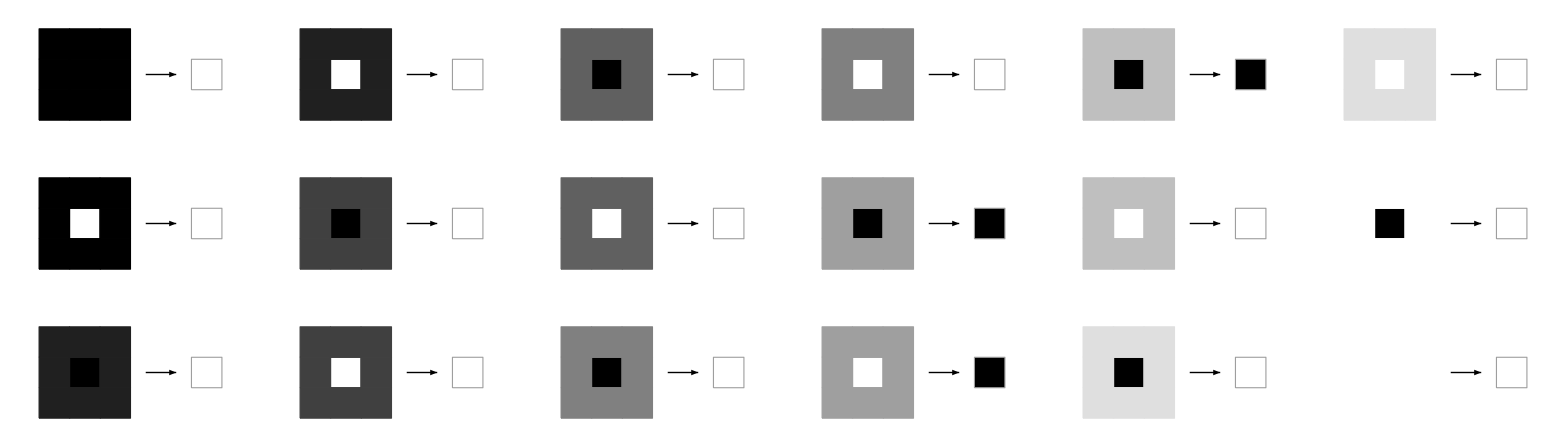

```mathematica
RulePlot[CellularAutomaton["GameOfLife"]]
```

```mathematica
CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}}]
```

CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}}]

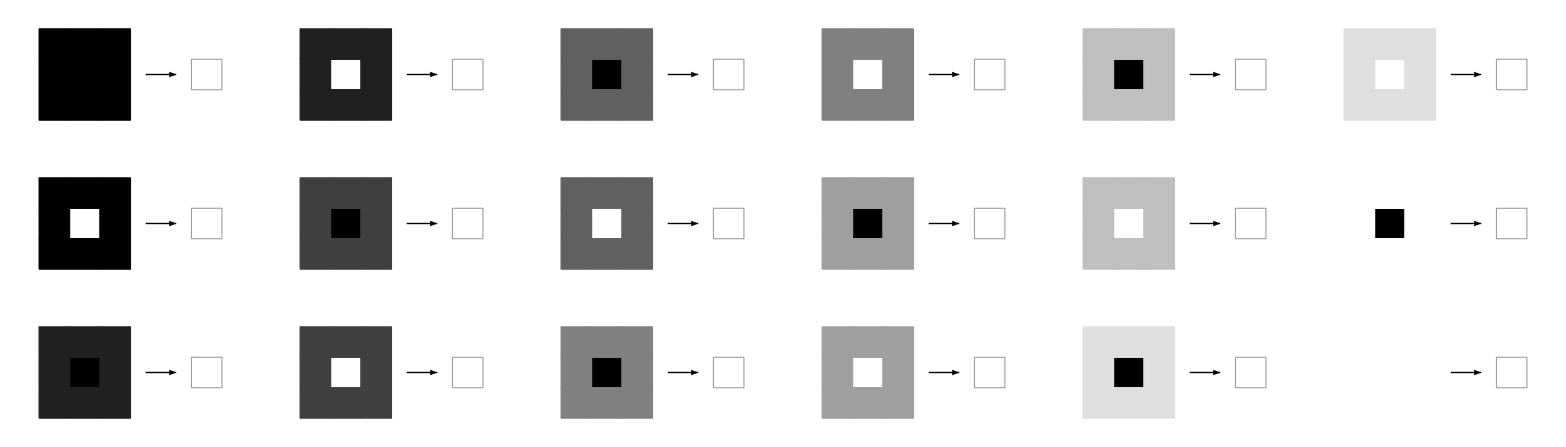

```mathematica
RulePlot[CellularAutomaton[{0,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}}]]
```

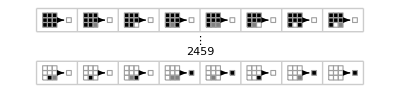

```mathematica
RulePlot[CellularAutomaton[{224,3,{1,1}}]]
```

```mathematica
3^7-1
```

2186

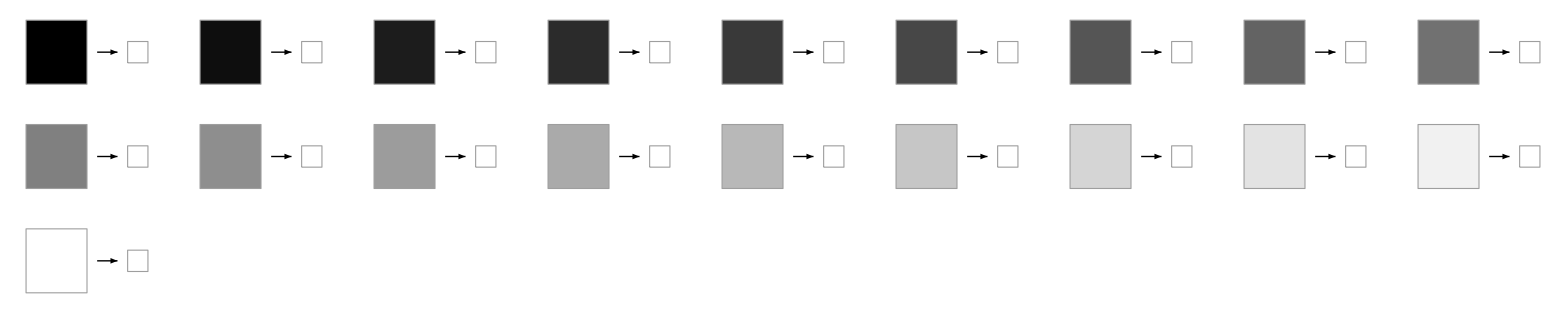

```mathematica
RulePlot[CellularAutomaton[{0,{3,1},{1,1}}]]
```

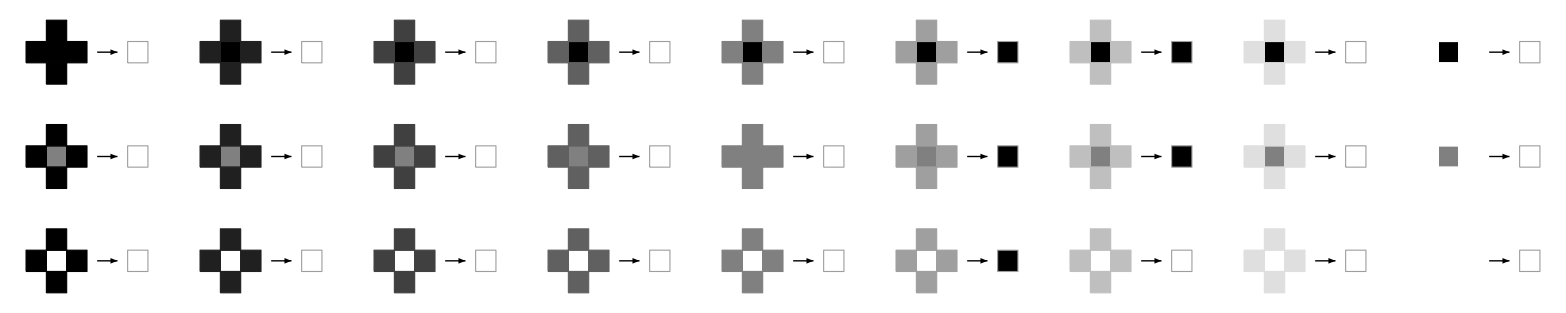

```mathematica
RulePlot[CellularAutomaton[{529254,{3,{{0,3,0},{3,1,3},{0,3,0}}},{1,1}}]]
```

```mathematica
List[{0,0,0,2,0,0,0,0,0},{0,0,1,1,0,0,0,0,0},{0,0,2,2,0,0,0,0,0}]
```

{{0,0,0,2,0,0,0,0,0},{0,0,1,1,0,0,0,0,0},{0,0,2,2,0,0,0,0,0}}

```mathematica
Transpose@{{0,0,0,2,0,0,0,0,0},{0,0,1,1,0,0,0,0,0},{0,0,2,2,0,0,0,0,0}}
```

{{0,0,0},{0,0,0},{0,1,2},{2,1,2},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Join@@{{0,0,0},{0,0,0},{0,1,2},{2,1,2},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}
```

{0,0,0,0,0,0,0,1,2,2,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Reverse[{0,0,0,0,0,0,0,1,2,2,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,2,2,1,0,0,0,0,0,0,0}

```mathematica
FromDigits[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,2,2,1,0,0,0,0,0,0,0},3]
```

468018

```mathematica
CellularAutomaton[{468018,{3,{{0,3,0},{3,1,3},{0,3,0}}},{1,1}},{{{2,2,0},{2,0,0},{0,0,1}},0},10]/2
```

{{{1,1,0},{1,0,0},{0,0,1/2}},{{0,1,0},{1,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
matrix=RandomInteger[2,{10,10}]
```

{{0,1,2,0,0,2,0,2,0,0},{0,2,0,2,0,0,2,2,2,1},{1,0,0,2,0,0,1,1,0,2},{2,0,1,0,2,2,2,0,2,0},{2,0,0,1,0,2,2,0,1,2},{1,1,2,0,0,2,1,2,1,0},{2,1,0,1,2,2,1,2,1,1},{1,2,0,0,2,1,0,1,1,1},{1,1,2,1,1,0,1,2,0,1},{0,2,2,0,0,1,2,1,2,2}}

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[{468018,{3,{{0,3,0},{3,1,3},{0,3,0}}},{1,1}},{matrix,0},10][[i]]],{i,1,10,1}]
```

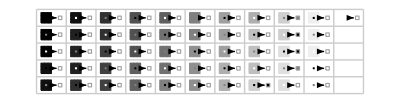

```mathematica
RulePlot[CellularAutomaton[{468018,{3,{{3,3,3},{3,1,3},{3,3,3}}},{1,1}}]]
```

```mathematica
k3ListsToRule[{{0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0}}]
```

468018

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[{468018,{3,{{3,3,3},{3,1,3},{3,3,3}}},{1,1}},{matrix,0},10][[i]]],{i,1,10,1}]
```

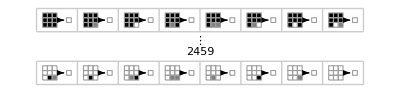

```mathematica
RulePlot[CellularAutomaton[{0,3,{1,1}}]]
```